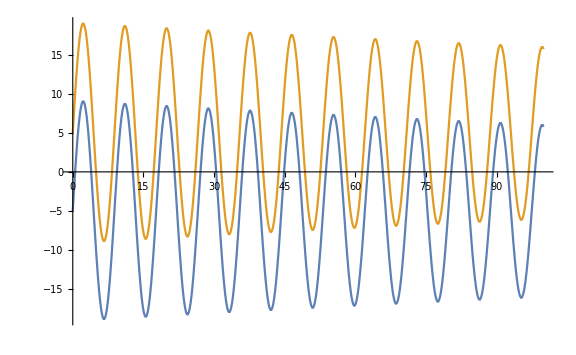

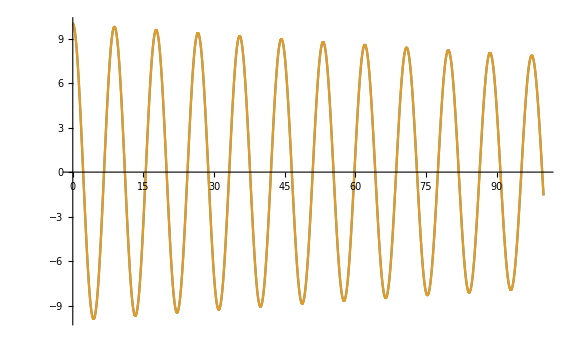

53361

```mathematica
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Aula8_2809/Results/";
data = Import[path <> "FewSprings.txt", "Data"];
x = {data[[All,{1,2}]], data[[All,{1,4}]]};
v = {data[[All,{1,3}]], data[[All,{1,5}]]};
ListLinePlot[x, ImageSize->Large]
ListLinePlot[v, ImageSize->Large]
(*Improvement: manipulate the four initial conditions: x0*x1*v1*v2 = 5*5*100*100*)
Length[Range[-10,10]]*Length[Range[-10,10]]*Length[Range[0,1,0.1]]*Length[Range[-1,0,0.1]]
(*A bit prohibitive to allow for all four parameters to vary like that*)
```

```mathematica
{(#-1)/4//N}&/@Range[1,10]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25}